```mathematica
(* 25.2.13 *)
```

```mathematica
(*<<NumericalMath`ListIntegrate` *)
```

```mathematica
Off[SetDelayed::"write"]
```

```mathematica
Directory[]


Off[General::spell1]
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];

 
(* 1  2   3  *)
(* nr,w,alpha,rh *)
conf=ReadList["res.txt",{Number,Number ,Number  ,Number   }]

 
nr=conf[[1]][[1]];
w= conf[[1]][[2]];
alfa= conf[[1]][[3]];
rh= conf[[1]][[4]];
  

Print["winding number n = ",nr];
Print["w   = ",w];
Print["alfa = ",alfa]; 
 Print["rh = ",rh]; 


gr=ReadList["gridx.dat",{Number}];


lgr=Length[gr];
nx=lgr;
Print["nx = ",nx];

listar=Table[gr[[k]][[1]],{k,1,lgr}] ;
listalogr=Table[Log[10,gr[[k]][[1]]],{k,1,lgr}];

 unghi0=ReadList["gridy.dat",{Number}];
ny=Length[unghi0];
Print["ny = ",ny];
unghi=Table[unghi0[[k]][[1]],{k,1,ny}]; 

(*unghi=Table[(k-1)*Pi/2/(ny-1),{k,1,ny}];*)

ntot=nx*ny;

a=ReadList["functf.dat",{Number,Number,Number,Number ,Number ,Number,Number,Number  }];


lung1=Length[a];


(*Datele sunt salvate direct cu indexarea globala*)
F1=Table[a[[k]][[1]],{k,1,lung1}];
F2=Table[a[[k]][[2]],{k,1,lung1}];
F0=Table[a[[k]][[3]],{k,1,lung1}];  
W=Table[a[[k]][[4]],{k,1,lung1}]; 
H1=Table[a[[k]][[5]],{k,1,lung1}];
H2=Table[a[[k]][[6]],{k,1,lung1}];
H3=Table[a[[k]][[7]],{k,1,lung1}];
V=Table[a[[k]][[8]],{k,1,lung1}];


(*Se construiesc ny liste pt. marimi de interes la unghiuri fixate *)
(*foarte util in reprezentari grafice *)

Do[

F1u[k]=Table[F1[[i]],{i,(k-1)*nx+1,k*nx}];
F2u[k]=Table[F2[[i]],{i,(k-1)*nx+1,k*nx}];
F0u[k]=Table[F0[[i]],{i,(k-1)*nx+1,k*nx}];  
Wu[k]=Table[W[[i]],{i,(k-1)*nx+1,k*nx}]; 
H1u[k]=Table[H1[[i]],{i,(k-1)*nx+1,k*nx}]; 
H2u[k]=Table[H2[[i]],{i,(k-1)*nx+1,k*nx}]; 
H3u[k]=Table[H3[[i]],{i,(k-1)*nx+1,k*nx}]; 
Vu[k]=Table[V[[i]],{i,(k-1)*nx+1,k*nx}]; 



,{k,1,ny}];
 
 
as1=2;
as2=IntegerPart[ny/2];
as3=ny-1;

sa1=3;
sa2=IntegerPart[nx/2];
sa3=nx-1;


Print["rmax = ",gr[[nx]][[1]]];
```

/home/h/usb/work/proca/HBHs/m=1.0/alpha=1.0/1st/w=0.980/rh=0.100

{{1.,0.98,1.,0.1}}

winding number n = 1.

w   = 0.98

alfa = 1.

rh = 0.1

nx = 261

ny = 35

rmax = 259.

```mathematica
minF0=Min[F0] 
maxF0=Max[ F0 ] 
minF1=Min[F1] 
maxF1=Max[ F1 ] 
minF2=Min[F2] 
maxF2=Max[ F2 ] 
minW=Min[W] 
maxW=Max[ W ] 
maxH1=Max[H1 ] 
minH1=Min[H1] 
maxH2=Max[H2 ] 
minH2=Min[H2] 
maxH3=Max[H3 ] 
minH3=Min[H3] 
maxV=Max[V ] 
minV=Min[V] 


f00=F0u[1][[1]]
f10=F1u[1][[1]]
f20=F2u[1][[1]] 

f0Pi2=F0u[ny][[1]]
f1Pi2=F1u[ny][[1]]
f2Pi2=F2u[ny][[1]]
```

-0.0679591

1.23937×10^-17

-1.23838×10^-17

0.0614334

-1.23849×10^-17

0.0673876

-2.44211×10^-17

0.0351496

0.0294463

-0.0069946

0.0925192

-0.0689858

0.0925192

-0.164064

0.000350117

-0.00260735

-0.062006

0.0614334

0.0614345

-0.0679591

0.0554803

0.0673876

```mathematica
n1=nx-1;

t1=Table[ {listar[[i]] ,E^(2*F0u[as1][[i]])},{i,2,n1}];
t2=Table[{ listar[[i]]  ,E^(2*F0u[as2][[i]])},{i,2,n1}];
t3=Table[{ listar[[i]] ,E^(2*F0u[as3][[i]])},{i,2,n1}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];

g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

as=Table[{  F0u[as3][[i]]},{i,2,n1}] ;
Min[F0]
```

-0.0679591

```mathematica
E^( 2Min[F0])
```

0.872914

```mathematica
n1=nx-1;

t1=Table[ {listar[[i]],  F0u[as1][[i]] },{i,2,n1}];
t2=Table[{ listar[[i]]  , F0u[as2][[i]] },{i,2,n1}];
t3=Table[{ listar[[i]] , F0u[as3][[i]]  },{i,2,n1}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];

g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

as=Table[{  F0u[as3][[i]]},{i,2,n1}] ;
Min[F0]
```

-0.0679591

```mathematica
cut=2;

t1=Table[{i,F1u[as1][[i]]},{i,1,lgr}];
t2=Table[{i,F1u[as2][[i]]},{i,1,lgr}];
t3=Table[{i,F1u[as3][[i]]},{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None,PlotJoined->True];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True,PlotJoined->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True,PlotJoined->True];

Print[" FUNCTION F1"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,F1u[as1][[i]]},{i,1,lgr-cut}];
t2=Table[{ listar[[i]]  ,F1u[as2][[i]]},{i,1,lgr-cut}];
t3=Table[{ listar[[i]] ,F1u[as3][[i]]},{i,1,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];

g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION F1

```mathematica
t1=Table[{i,F2u[as1][[i]]},{i,1,lgr}];
t2=Table[{i,F2u[as2][[i]]},{i,1,lgr}];
t3=Table[{i,F2u[as3][[i]]},{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION F2"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];


t1=Table[ {listar[[i]] ,F2u[as1][[i]]},{i,1,lgr-cut}];
t2=Table[{ listar[[i]]  ,F2u[as2][[i]]},{i,1,lgr-cut}];
t3=Table[{ listar[[i]] ,F2u[as3][[i]]},{i,1,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];

g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION F2

```mathematica
t1=Table[{i,F0u[as1][[i]]},{i,1,lgr}];
t2=Table[{i,F0u[as2][[i]]},{i,1,lgr}];
t3=Table[{i,F0u[as3][[i]]},{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION F0"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];


t1=Table[ {listar[[i]] ,F0u[as1][[i]]},{i,2,lgr-cut}];
t2=Table[{ listar[[i]]  ,F0u[as2][[i]]},{i,2,lgr-cut}];
t3=Table[{ listar[[i]] ,F0u[as3][[i]]},{i,2,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];

g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION F0

```mathematica
cut=1;
```

```mathematica
t1=Table[{i,Wu[as1][[i]] },{i,1,lgr}];
t2=Table[{i,Wu[as2][[i]] },{i,1,lgr}];
t3=Table[{i,Wu[as3][[i]] },{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION W"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,Wu[as1][[i]]},{i,1,lgr-cut}];
t2=Table[{ listar[[i]]  ,Wu[as2][[i]]},{i,1,lgr-cut}];
t3=Table[{ listar[[i]] ,Wu[as3][[i]]},{i,1,lgr-cut}];;

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION W

```mathematica
t1=Table[{i,H1u[as1][[i]] },{i,1,lgr}];
t2=Table[{i,H1u[as2][[i]] },{i,1,lgr}];
t3=Table[{i,H1u[as3][[i]] },{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION H1"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,H1u[as1][[i]]/listar[[i]]},{i,2,lgr-cut}];
t2=Table[{ listar[[i]]  , H1u[as2][[i]]/listar[[i]]},{i,2,lgr-cut}];
t3=Table[{ listar[[i]] ,H1u[as3][[i]]/listar[[i]]},{i,2,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION H1

```mathematica
t1=Table[{i,H1u[as1][[i]] },{i,1,20}];
t2=Table[{i,H1u[as2][[i]] },{i,1,20}];
t3=Table[{i,H1u[as3][[i]] },{i,1,20}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION H1"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,H1u[as1][[i]] },{i,2,20}];
t2=Table[{ listar[[i]]  , H1u[as2][[i]] },{i,2,20}];
t3=Table[{ listar[[i]] ,H1u[as3][[i]] },{i,2,20}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION H1

```mathematica
t1=Table[{i,H1u[as1][[i]] },{i,1,lgr}];
t2=Table[{i,H1u[as2][[i]] },{i,1,lgr}];
t3=Table[{i,H1u[as3][[i]] },{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION H1"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,H1u[as1][[i]]},{i,2,lgr-cut}];
t2=Table[{ listar[[i]]  ,H1u[as2][[i]]},{i,2,lgr-cut}];
t3=Table[{ listar[[i]] ,H1u[as3][[i]]},{i,2,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION H1

```mathematica
t1=Table[{i,H2u[as1][[i]] },{i,1,lgr}];
t2=Table[{i,H2u[as2][[i]] },{i,1,lgr}];
t3=Table[{i,H2u[as3][[i]] },{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION H2"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,H2u[as1][[i]]},{i,2,lgr-cut}];
t2=Table[{ listar[[i]]  ,H2u[as2][[i]]},{i,2,lgr-cut}];
t3=Table[{ listar[[i]] ,H2u[as3][[i]]},{i,2,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION H2

```mathematica
t1=Table[{i,H3u[as1][[i]] },{i,1,lgr}];
t2=Table[{i,H3u[as2][[i]] },{i,1,lgr}];
t3=Table[{i,H3u[as3][[i]] },{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION H3"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,H3u[as1][[i]]},{i,2,lgr-cut}];
t2=Table[{ listar[[i]] ,H3u[as2][[i]]},{i,2,lgr-cut}];
t3=Table[{ listar[[i]] ,H3u[as3][[i]]},{i,2,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION H3

```mathematica
t1=Table[{i,Vu[as1][[i]] },{i,1,lgr}];
t2=Table[{i,Vu[as2][[i]] },{i,1,lgr}];
t3=Table[{i,Vu[as3][[i]] },{i,1,lgr}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION V"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];

t1=Table[ {listar[[i]] ,Vu[as1][[i]]},{i,2,lgr-cut}];
t2=Table[{ listar[[i]]  ,Vu[as2][[i]]},{i,2,lgr-cut}];
t3=Table[{ listar[[i]] ,Vu[as3][[i]]},{i,2,lgr-cut}];

g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity,  Frame->True ,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True ];
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION V

```mathematica
Do[
qs[k]=ListPlot[F1u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["F1: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

F1: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[F2u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["F2: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

F2: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[F0u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["F0: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

F0: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[Wu[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["W: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

W: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[H1u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["H1: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

H1: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[H2u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["H2: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

H2: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[H3u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["H3: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

H3: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[Vu[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["V: r-varies; ny angular directions "];
Show[  qs[1],qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34],qs[35]   , DisplayFunction->$DisplayFunction]
```

V: r-varies; ny angular directions

-Graphics-

```mathematica
(*Do[
Print["z =",i,"  ",unghi[[i]]];
ListPlot[F0u[i],PlotRange->All,Axes->None,Frame->True,Prolog->AbsolutePointSize[4] ]
,{i,1,ny}]*)
```

```mathematica
ni=100;

cut= 1;
t1=Table[{listar[[i]], listar[[i]] (F0u[as1][[i]] ) },{i,ni,lgr- cut}];
t2=Table[{listar[[i]], listar[[i]] (F0u[as2][[i]]  ) },{i,ni,lgr- cut}];
t3=Table[{listar[[i]], listar[[i]] (F0u[as3][[i]]   )},{i,ni,lgr- cut}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION F01(theta)"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION F01(theta)

```mathematica
t1=Table[{listar[[i]], listar[[i]] (F1u[as1][[i]] ) },{i,ni,lgr-cut}];
t2=Table[{listar[[i]], listar[[i]] (F1u[as2][[i]]  ) },{i,ni,lgr-cut}];
t3=Table[{listar[[i]], listar[[i]] (F1u[as3][[i]]   )},{i,ni,lgr-cut}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION F11(theta)"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION F11(theta)

```mathematica
cut
```

1

```mathematica
t1=Table[{listar[[i]], listar[[i]] (F2u[as1][[i]] ) },{i,ni,lgr-cut}];
t2=Table[{listar[[i]], listar[[i]] (F2u[as2][[i]]  ) },{i,ni,lgr-cut}];
t3=Table[{listar[[i]], listar[[i]] (F2u[as3][[i]]   )},{i,ni,lgr-cut}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION F21(theta)"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION F21(theta)

```mathematica
t1=Table[{listar[[i]], listar[[i]]  (Wu[as1][[i]] ) },{i,ni,lgr-cut}];
t2=Table[{listar[[i]], listar[[i]] (Wu[as2][[i]]  ) },{i,ni,lgr-cut}];
t3=Table[{listar[[i]], listar[[i]]  (Wu[as3][[i]]   )},{i,ni,lgr-cut}];


g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity,  Frame->True];

Print[" FUNCTION W2(theta)"]
Show[g1,g2,g3,DisplayFunction->$DisplayFunction,Prolog->AbsolutePointSize[4]];
```

FUNCTION W2(theta)

```mathematica
cut
```

1

{{1,-0.649409},{2,-0.649414},{3,-0.649428},{4,-0.64945},{5,-0.649482},{6,-0.649522},{7,-0.64957},{8,-0.649626},{9,-0.64969},{10,-0.64976},{11,-0.649836},{12,-0.649918},{13,-0.650005},{14,-0.650096},{15,-0.65019},{16,-0.650287},{17,-0.650386},{18,-0.650485},{19,-0.650585},{20,-0.650683},{21,-0.65078},{22,-0.650875},{23,-0.650966},{24,-0.651053},{25,-0.651135},{26,-0.651212},{27,-0.651283},{28,-0.651346},{29,-0.651403},{30,-0.651451},{31,-0.651492},{32,-0.651523},{33,-0.651546},{34,-0.65156},{35,-0.651565}}

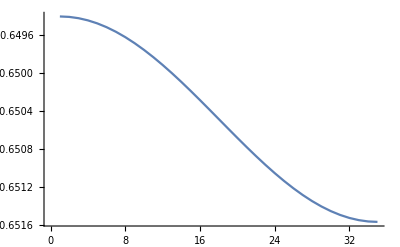

```mathematica
nf=nx- cut;
ti=Table[{i, listar[[nf]] (F0u[i][[nf]] ) },{i,1,ny}]
ListPlot[ti,PlotJoined->True]
```

{{1,1.27803},{2,1.27807},{3,1.2782},{4,1.27842},{5,1.27872},{6,1.27911},{7,1.27958},{8,1.28012},{9,1.28073},{10,1.28141},{11,1.28214},{12,1.28294},{13,1.28378},{14,1.28466},{15,1.28557},{16,1.28651},{17,1.28747},{18,1.28843},{19,1.2894},{20,1.29036},{21,1.2913},{22,1.29223},{23,1.29312},{24,1.29397},{25,1.29477},{26,1.29552},{27,1.29621},{28,1.29684},{29,1.29739},{30,1.29787},{31,1.29826},{32,1.29857},{33,1.2988},{34,1.29893},{35,1.29898}}

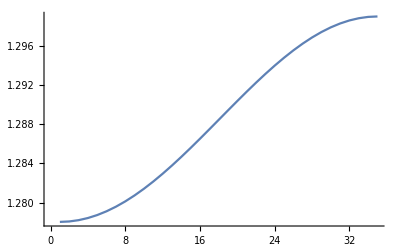

```mathematica
nf=nx- cut;
ti=Table[{i, listar[[nf]] (Wu[i][[nf]] ) },{i,1,ny}]
ListPlot[ti,PlotJoined->True]
```

```mathematica
ct=1;
cut=1;

ini=5; 

Do[

data=Table[{listar[[i]] ,F0u[k][[i]]   },{i,nx-ini,nx-cut}];
u=Fit[data,{ 1/x ,1/x^2  ,1/x^3   } ,x];
cf01[k ]=Coefficient[u,1/x ];

data=Table[{listar[[i]] ,F1u[k][[i]]   },{i,nx-ini,nx-cut}];
u=Fit[data,{1/x ,1/x^2  ,1/x^3     } ,x]; 
cf11[k ]=Coefficient[u,1/x ];


data=Table[{listar[[i]] ,F2u[k][[i]]   },{i,nx-ini,nx-cut}];
u=Fit[data,{1/x ,1/x^2  ,1/x^3   } ,x];
cf21[k ]=Coefficient[u,1/x];

 data=Table[{listar[[i]] ,Wu[k][[i]]   },{i,nx-ini,nx-cut}];
u=Fit[data,{1/x ,1/x^2, 1/x^3} ,x];
cW[k ]=Coefficient[u,1/x  ];

,{k,1,ny }]

f01=Table[cf01[k],{k,1,ny }] ;
f11=Table[cf11[k],{k,1,ny }] ;
f21=Table[cf21[k],{k,1,ny }] ;
W3=Table[cW[k],{k,1,ny }] ;
```

```mathematica
1-Max[f01]/Min[f01]
1-Max[f11]/Min[f11]
1-Max[f21]/Min[f21]
1-Max[W3]/Min[W3]
```

0.00236846

-0.00239789

-0.00241114

-0.0285817

```mathematica
f01
1+(2f01+f11 )/(f21)
```

{-0.65163,-0.65162,-0.651593,-0.651548,-0.651486,-0.651409,-0.651318,-0.651216,-0.651105,-0.650988,-0.650867,-0.650746,-0.650627,-0.650514,-0.650409,-0.650315,-0.650235,-0.650171,-0.650124,-0.650096,-0.650086,-0.650095,-0.650122,-0.650165,-0.650222,-0.650289,-0.650365,-0.650444,-0.650523,-0.650599,-0.650666,-0.650723,-0.650765,-0.650792,-0.650801}

{-2.93702×10^-6,-3.08897×10^-6,-3.54141×10^-6,-4.28598×10^-6,-5.31×10^-6,-6.59793×10^-6,-8.13344×10^-6,-9.90194×10^-6,-0.0000118933,-0.0000141046,-0.0000165429,-0.0000192275,-0.0000221914,-0.0000254821,-0.0000291607,-0.0000333001,-0.000037981,-0.0000432864,-0.0000492946,-0.0000560705,-0.0000636564,-0.0000720621,-0.0000812558,-0.0000911564,-0.000101629,-0.000112482,-0.000123471,-0.000134306,-0.000144662,-0.000154197,-0.00016257,-0.000169464,-0.000174604,-0.000177779,-0.000178854}

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
 crucial numerical test 
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

test1=1+(2f01+f11 )/(f21);
ListPlot[test1,PlotRange->All, Frame->True,Axes->None,PlotJoined->True];

err1=Max[Abs[test1]]
```

0.000178854

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
PRELUCRARE  DATA infinity
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)


dat=ReadList["fx-inf.txt",{Number,Number ,Number ,Number,Number ,Number  ,Number ,Number ,Number }];
lung1=Length[dat] ;

r=Table[dat[[i]][[1]],{i,1,lung1}];
infF1=Table[dat[[i]][[2]],{i,1,lung1}]
infF2=Table[dat[[i]][[3]],{i,1,lung1}];
infF0=Table[dat[[i]][[4]],{i,1,lung1}]
infW=Table[dat[[i]][[5]],{i,1,lung1}];
```

{-0.650544,-0.650545,-0.650548,-0.650552,-0.650558,-0.650565,-0.650574,-0.650584,-0.650595,-0.650606,-0.650618,-0.65063,-0.650642,-0.650653,-0.650664,-0.650673,-0.650681,-0.650687,-0.650692,-0.650694,-0.650694,-0.650693,-0.650689,-0.650684,-0.650677,-0.650669,-0.65066,-0.650651,-0.650642,-0.650633,-0.650625,-0.650618,-0.650613,-0.65061,-0.650609}

{0.65063,0.65063,0.650633,0.650637,0.650643,0.650651,0.650659,0.650669,0.65068,0.650692,0.650704,0.650716,0.650728,0.650739,0.65075,0.650759,0.650767,0.650774,0.650778,0.650781,0.650781,0.65078,0.650776,0.650771,0.650764,0.650756,0.650747,0.650737,0.650727,0.650718,0.65071,0.650703,0.650698,0.650695,0.650694}

```mathematica
constINF=Sum[infF0[[i]],{i,1,ny}]/ny
Max[infF0]/Min[infF0]

 constJINF=Sum[infW[[i]],{i,1,ny}]/ny

Max[infW]/Min[infW]
```

0.650717

1.00023

-1.30422

0.99794

```mathematica
0.96,1.0496655340016046
```

```mathematica
w
```

0.98

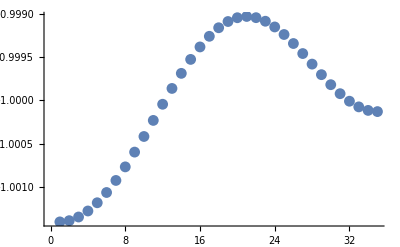

```mathematica
ListPlot[f01/constINF]
```

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
PRELUCRARE  DATA infinity - second dervatives
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)


dat=ReadList["fxx-inf.txt",{Number,Number ,Number ,Number,Number ,Number  ,Number ,Number ,Number }];
lung1=Length[dat] ;

r=Table[dat[[i]][[1]],{i,1,lung1}];
infF1xx=Table[dat[[i]][[2]],{i,1,lung1}];
infF2xx=Table[dat[[i]][[3]],{i,1,lung1}];
infF0xx=Table[dat[[i]][[4]],{i,1,lung1}];
infWxx=Table[dat[[i]][[5]],{i,1,lung1}]
```

{-0.269664,-0.282072,-0.319182,-0.380625,-0.465772,-0.573696,-0.703141,-0.852474,-1.01965,-1.20219,-1.39713,-1.60107,-1.81016,-2.02019,-2.22664,-2.42484,-2.61011,-2.77795,-2.92426,-3.0455,-3.13898,-3.20302,-3.23708,-3.24192,-3.21963,-3.17356,-3.10824,-3.02915,-2.94244,-2.8546,-2.77205,-2.70075,-2.64582,-2.61118,-2.59932}

```mathematica
Mx=Sum[infF0[[i]],{i,1,ny}]/ny
```

0.650717

```mathematica
Mxx=-Sum[infF0xx[[i]],{i,1,ny}]/ny/2
```

0.685664

```mathematica
Jxx=Sum[infWxx[[i]],{i,1,ny}]/ny
```

-2.09669

```mathematica
Jinterpol=Sum[W3[[i]],{i,1,ny}]/ny
Minterpol=Sum[f01[[i]],{i,1,ny}]/ny;
```

1.30786

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%% 
computation Mass from asymptotics
 %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

(* th result:*) 
(*
Series[-g[4,4],{r,Infinity,1}]
1+(2 const-rh)/r+O[1/r]^2
*)

const=Sum[f01[[i]],{i,1,ny}]/ny;

Mc=  constINF;

MSch=rh/2 ;
Mass=MSch+Mc;

Print["Mass Schw     = ",MSch];
Print["Mass correction= ",Mc];
Print["total Mass     = ",Mass];

(*Print[ MSAdS/Mc]*)
```

Mass Schw     = 0.05

Mass correction= 0.650717

total Mass     = 0.700717

317

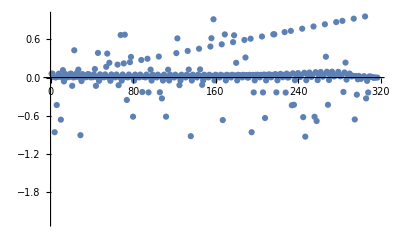

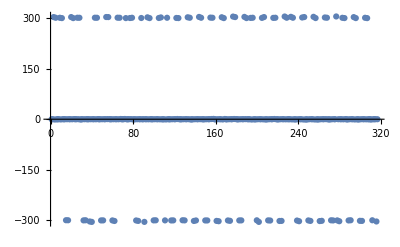

305.873

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
PRELUCRARE  DATA t-0 -- no conical singularities
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)


dat=ReadList["f-t0.txt",{Number,Number ,Number ,Number,Number,Number ,Number ,Number ,Number  }];
lung1=Length[dat] 

r=Table[dat[[i]][[1]],{i,1,lung1}];
t0F1=Table[dat[[i]][[2]],{i,1,lung1}];
t0F2=Table[dat[[i]][[3]],{i,1,lung1}];
t0F0=Table[dat[[i]][[4]],{i,1,lung1}];
t0W=Table[dat[[i]][[5]],{i,1,lung1}];
t0H1=Table[dat[[i]][[6]],{i,1,lung1}];
t0H2=Table[dat[[i]][[7]],{i,1,lung1}];
t0H3=Table[dat[[i]][[8]],{i,1,lung1}];
t0V=Table[dat[[i]][[9]],{i,1,lung1}];

ratio= t0F2-t0F1;
ListPlot[t0F2]
ListPlot[ratio]
Max[ratio]
```

Power::infy: Infinite expression 1/0. encountered.

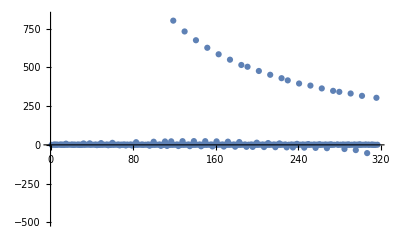

```mathematica
ListPlot[1-t0H2/t0H3]
```

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
PRELUCRARE r=0 DATA
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)


dat=ReadList["f-0.txt",Number,RecordLists->True];
lung1=Length[dat] ;

unghi=Table[dat[[i]][[1]],{i,1,lung1}];
hF1=Table[dat[[i]][[2]],{i,1,lung1}]; 
hF2=Table[dat[[i]][[3]],{i,1,lung1}]; 
hF0=Table[dat[[i]][[4]],{i,1,lung1}]; 
hW=Table[dat[[i]][[5]],{i,1,lung1}]; 
hH1=Table[dat[[i]][[6]],{i,1,lung1}];
hH2=Table[dat[[i]][[7]],{i,1,lung1}];
hH3=Table[dat[[i]][[8]],{i,1,lung1}];
hV=Table[dat[[i]][[9]],{i,1,lung1}];  


(*%%%%%%% Hawking temperature %%%%%%%%*)
TH0=1/(4 Pi rh) ;

THc=  1/lung1 Sum[ E^( (hF0[[i]]-hF1[[i]])),{i,1,lung1}];(* correction due to the scalar field*)
TH=TH0 THc;
Print["Schw temp. TH0= ",TH0]
Print["correction THc= ",THc]
Print["TH= ",TH]


errTH=1-Abs[Min[hF0-hF1] /Max[hF0-hF1]];
Print["error TH= ",errTH//N]
```

Schw temp. TH0= 0.795775

correction THc= 0.883875

TH= 0.703366

error TH= -9.42314×10^-8

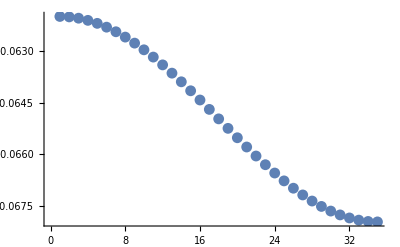

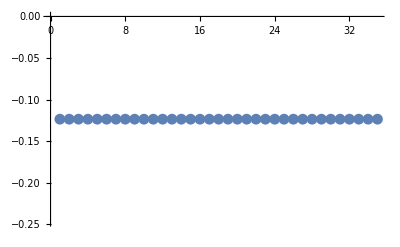

```mathematica
ListPlot[hF0 ]

(* this is to check the constancy of the Hawking temp *)
ListPlot[hF0-hF1]
```

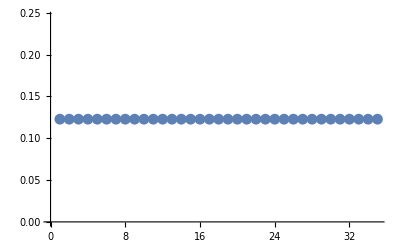

```mathematica
(* angular dependence of the entropy corrections *)
 ListPlot[hF1+hF2]
```

```mathematica
(*%%%%%%% event horizon area %%%%%%%%*)
AH0=4 Pi rh^2;
 iAHc=Table[{unghi[[k]],1/2  Sin[unghi[[k]]] E^((hF1[[k]] +hF2[[k]] )) },{k,1,lung1 }];

(* 2 because I integrate between 0, Pi/2 *)
 AHc= 2Integrate[Interpolation[iAHc,InterpolationOrder->1][x],{x,0,Pi/2}];

AH=AH0 AHc;

Print["Schw area  AH0= ",AH0];
Print["correction AHc= ",AHc];
Print["Event horizon area =",AH];
```

Schw area  AH0= 0.125664

correction AHc= 1.13053

Event horizon area =0.142067

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
computation Le, Lp -- see MATH code for derivation
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

(*Le=2 ⅇ^F2[0,π/2] π rH*)
Le=2 ⅇ^hF2[[ny]] π rh;
Print["Le = ",Le ];

(*Lp=2 ∫_0^π ⅇ^F1[0,t] rHⅆt*)
Lp1= Table[{unghi[[k]],2 rh    ⅇ^hF1[[k]]   },{k,1,lung1 }];
(*Lp=  2ListIntegrate[Lp1,2]//N;(*factor 2: because I integrate [0,pi/2]*) *)
Lp=2 Integrate[Interpolation[Lp1,InterpolationOrder->3][x],{x,Min[Lp1[[All,1]]],Max[Lp1[[All,1]]]}];
Print["Lp = ",Lp ];
Print["  " ];
```

Le = 0.672119

Lp = 0.666147

```mathematica
Le/Lp
```

1.00896

```mathematica
OmegaH
```

OmegaH

```mathematica
rh
```

0.1

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%% 
 computation MASS from the energy momentum tensor   %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

asa1=2;
asa2=IntegerPart[ny/2];
asa3=ny-1;


 (* ordinea este: {T34,T44,Ttot,J4}  *)
q=ReadList["T44.dat",{Number,Number,Number,Number }];
lungq=Length[q];

diference=lungq-ntot;
Print["It must be zero! ",diference];
 

T34=Table[q[[k]][[1]],{k,1,lungq}]; 
ro=Table[q[[k]][[2]],{k,1,lungq}]; 
 Ttot=Table[q[[k]][[3]],{k,1,lungq}]; 
J4=Table[q[[k]][[4]],{k,1,lungq}]; 

(*Se construiesc ny liste pt. marimi de interes la unghiuri fixate *)
(*foarte util in reprezentari grafice *)

Do[ 
T34u[k]=Table[T34[[i]],{i,(k-1)*nx+1,k*nx}]; 
rou[k]=Table[ro[[i]],{i,(k-1)*nx+1,k*nx}]; 
Ttotu[k]=Table[Ttot[[i]],{i,(k-1)*nx+1,k*nx}]; 
J4u[k]=Table[J4[[i]],{i,(k-1)*nx+1,k*nx}]; 
(*	Print[T44u[k]];*)
,{k,1,ny}]

 
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
 now I plot the energy density for three different angles
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

ni=2;
cut= 8;

t1=Table[{listar[[i]],-rou[asa1][[i]] },{i,ni,nx-cut}];
t2=Table[{listar[[i]],-rou[asa2][[i]] },{i,ni,nx-cut}];
t3=Table[{listar[[i]],-rou[asa3][[i]] },{i,ni,nx-cut}];
 
g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None ,PlotJoined->True];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ,PlotJoined->True, PlotStyle->{RGBColor[1,0,0]}];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity, Frame->True ,PlotJoined->True, PlotStyle->{RGBColor[1,1,0]}];
  Print["black: theta=0 "]; 

 Print["profiles energy density"];
 Show[g1,g2,g3,DisplayFunction->$DisplayFunction];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
 now I plot the constraint T34 for three different angles
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
t1=Table[{listar[[i]],T34u[asa1][[i]] },{i,ni,nx-cut}];
t2=Table[{listar[[i]],T34u[asa2][[i]] },{i,ni,nx-cut}];
t3=Table[{listar[[i]],T34u[asa3][[i]] },{i,ni,nx-cut}];	
 
g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None ,PlotJoined->True,PlotRange->All];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ,PlotJoined->True, PlotStyle->{RGBColor[1,0,0]}];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity, Frame->True ,PlotJoined->True, PlotStyle->{RGBColor[1,1,0]}];
(* Print["black: theta=0 "];*)

 Print["profiles T34"];
 Show[g1,g2,g3,DisplayFunction->$DisplayFunction];


(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
 now I plot the constraint J4 for three different angles
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
t1=Table[{listar[[i]],J4u[asa1][[i]] },{i,ni,nx-cut}];
t2=Table[{listar[[i]],J4u[asa2][[i]] },{i,ni,nx-cut}];
t3=Table[{listar[[i]],J4u[asa3][[i]] },{i,ni,nx-cut}];	
 
g1=ListPlot[t1,PlotRange->All,DisplayFunction->Identity, Frame->True,Axes->None ,PlotJoined->True,PlotRange->All];
g2=ListPlot[t2,PlotRange->All,DisplayFunction->Identity, Frame->True ,PlotJoined->True, PlotStyle->{RGBColor[1,0,0]}];
g3=ListPlot[t3,PlotRange->All,DisplayFunction->Identity, Frame->True ,PlotJoined->True, PlotStyle->{RGBColor[1,1,0]}];
 Print["black: theta=0 "]; 

 Print["profiles J4"];
 Show[g1,g2,g3,DisplayFunction->$DisplayFunction];



(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
 now I compute the Proca field contribution to the total mass
& Smarr law&etc
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
(* sqrt = ⅇ^(F0[r,t]+2 F1[r,t]+F2[r,t]) r^2 Sin[t]*)

(*Se construiesc ny liste pt. integralele marimilor de interes la unghiuri fixate *)

Do[

 Mio2[k]=Table[{listar[[i]],  ⅇ^(F0u[k][[i]]+2 F1u[k][[i]]+F2u[k][[i]])  listar[[i]]  √(listar[[i]]^2+rh^2)Ttotu[k][[i]]},{i,ni,nx-1}];
 Mio3[k]=Table[{listar[[i]], ⅇ^(F0u[k][[i]]+2 F1u[k][[i]]+F2u[k][[i]])  listar[[i]]  √(listar[[i]]^2+rh^2)  T34u[k][[i]]},{i,ni,nx-1}];
 Mio4[k]=Table[{listar[[i]],  ⅇ^(F0u[k][[i]]+2 F1u[k][[i]]+F2u[k][[i]])  listar[[i]]  √(listar[[i]]^2+rh^2)  J4u[k][[i]]},{i,ni,nx-1}];


,{k,2,ny-1}];



(*Se construiesc ny liste pt. integralele marimilor de interes la unghiuri fixate *)
Do[
(*Ma2[k]=ListIntegrate[Mio2[k],2]//N;
Ma3[k]=ListIntegrate[Mio3[k],2]//N;
Ma4[k]=ListIntegrate[Mio4[k],2]//N;*)
Ma2[k]=Integrate[Interpolation[Mio2[k]1,InterpolationOrder->3][x],{x,Min[Mio2[k][[All,1]]],Max[Mio2[k][[All,1]]]}]//N;
Ma3[k]=Integrate[Interpolation[Mio3[k]1,InterpolationOrder->3][x],{x,Min[Mio3[k][[All,1]]],Max[Mio3[k][[All,1]]]}]//N;
Ma4[k]=Integrate[Interpolation[Mio4[k]1,InterpolationOrder->3][x],{x,Min[Mio4[k][[All,1]]],Max[Mio4[k][[All,1]]]}]//N;

 ,{k,2,ny-1}];

 
Ma2[1]=Ma2[2];
Ma2[ny]=Ma2[ny-1];
 
Ma3[1]=Ma3[2];
Ma3[ny]=Ma3[ny-1];

Ma4[1]=Ma4[2];
Ma4[ny]=Ma4[ny-1];


 Minn2=Table[{unghi[[k]], Sin[unghi[[k]]] Ma2[k]},{k,1,ny}];
  Minn3=Table[{unghi[[k]], Sin[unghi[[k]]] Ma3[k]},{k,1,ny}];
  Minn4=Table[{unghi[[k]], Sin[unghi[[k]]] Ma4[k]},{k,1,ny}];

 (*Mint=-ListIntegrate[Minn2,2]//N; 
Jint=ListIntegrate[Minn3,2]//N; 
Q=ListIntegrate[Minn4,2]//N; *)
Mint=Integrate[Interpolation[Minn2,InterpolationOrder->3][x],{x,Min[Minn2[[All,1]]],Max[Minn2[[All,1]]]}]//N;
Jint=Integrate[Interpolation[Minn3,InterpolationOrder->3][x],{x,Min[Minn3[[All,1]]],Max[Minn3[[All,1]]]}]//N;
Q=Integrate[Interpolation[Minn4,InterpolationOrder->3][x],{x,Min[Minn4[[All,1]]],Max[Minn$[[All,1]]]}]//N;


 Print["Mintegral = ",Mint];  
 Print["Jintegral = ",Jint];  
 Print["Q = ",Q];
```

It must be zero! 0

black: theta=0

profiles energy density

profiles T34

black: theta=0

profiles J4

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

NIntegrate::nlim: x = Symbol[] is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Mintegral = -0.674751

Jintegral = 0.738343

NIntegrate::nlim: x = Symbol[] is not a valid limit of integration.

Q = NIntegrate[InterpolatingFunction[{{0., 1.5708}}, <>][x],{x,0.,Symbol[]}]

```mathematica
1-Jint/Q
```

NIntegrate::nlim: x = Symbol[] is not a valid limit of integration.

1-0.738343/NIntegrate[InterpolatingFunction[{{0., 1.5708}}, <>][x],{x,0.,Symbol[]}]

```mathematica
Do[
qs[k]=ListPlot[-rou[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["T_t^t: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

T_t^t: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[T34u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["T_fi^t: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

T_fi^t: r-varies; ny angular directions

-Graphics-

```mathematica
t1=Table[{listar[[i]],T34u[3][[i]] },{i,3,nx-cut}];
  
g1=ListPlot[t1,PlotRange->All,  Frame->True,Axes->None ,PlotJoined->True,PlotRange->All];
```

```mathematica
ny
```

35

```mathematica
Do[
qs[k]=ListPlot[ J4u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print[" Jt: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

Jt: r-varies; ny angular directions

-Graphics-

```mathematica
roH=Table[{unghi[[k]],-rou[k][[2]]},{k,2,ny-1}]; ListPlot[roH,PlotRange->All, Frame->True,Axes->None,PlotJoined->True];
```

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%% 
plot quantities which show the quality of numerics
   %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

 
 (* ordinea este: {Eq11,Eq12,Ricci,Kr, gauge}  *)
q=ReadList["eq1.dat",{Number,Number,Number,Number,Number  } ];
lungq=Length[q];

diference=lungq-ntot;
Print["It must be zero! ",diference];
 

Eq11=Table[q[[k]][[1]],{k,1,lungq}]; 
Eq12=Table[q[[k]][[2]],{k,1,lungq}]; 
 Ricci=Table[q[[k]][[3]],{k,1,lungq}]; 
Kr=Table[q[[k]][[4]],{k,1,lungq}];  
gauge=Table[q[[k]][[5]],{k,1,lungq}]; (*it should be zero*)

(*Se construiesc ny liste pt. marimi de interes la unghiuri fixate *)
(*foarte util in reprezentari grafice *)

Do[ 
Eq11u[k]=Table[Eq11[[i]],{i,(k-1)*nx+1,k*nx}]; 
Eq12u[k]=Table[Eq12[[i]],{i,(k-1)*nx+1,k*nx}]; 
 Ricciu[k]=Table[Ricci[[i]],{i,(k-1)*nx+1,k*nx}]; 
 Kru[k]=Table[Kr[[i]],{i,(k-1)*nx+1,k*nx}]; 
 gaugeu[k]=Table[gauge[[i]],{i,(k-1)*nx+1,k*nx}]; 
 
,{k,1,ny}]
```

It must be zero! 0

```mathematica
Do[
qs[k]=ListPlot[Eq11u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["Eq11: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

Eq11: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[Eq12u[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["Eq12: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

Eq12: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[ Ricciu[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print[" Ricci R: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

Ricci R: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[ Kru[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print[" Kr: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

Kr: r-varies; ny angular directions

-Graphics-

```mathematica
Do[
qs[k]=ListPlot[ gaugeu[k] ,Axes->None, Frame->True,Prolog->AbsolutePointSize[3],DisplayFunction->Identity,PlotRange->All];,
{k,1,ny}]

Print["  gauge: r-varies; ny angular directions "];
Show[ qs[2],qs[3],qs[4],qs[5],qs[6],qs[7],qs[8],qs[9],qs[10], qs[11],qs[12],qs[13],qs[14],qs[15],qs[16],qs[17],qs[18],qs[19],qs[20],qs[21],qs[22],qs[23],qs[24],qs[25],qs[26],qs[27],qs[28],qs[29],qs[30],qs[31],qs[32],qs[33],qs[34]   , DisplayFunction->$DisplayFunction]
```

gauge: r-varies; ny angular directions

-Graphics-

```mathematica
Max[Abs[Eq11]]
Max[Abs[Eq12]]
Max[Abs[gauge]]
```

0.000406176

0.00180274

0.0033809

```mathematica
constJINF
```

-1.30422

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
computation MH, JH -- see MATH code for derivation
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
dat=ReadList["fxx-0.txt",{Number,Number ,Number ,Number,Number ,Number ,Number ,Number ,Number  }];
lung1=Length[dat] ;

unghi=Table[dat[[i]][[1]],{i,1,lung1}];
hF1xx=Table[dat[[i]][[2]],{i,1,lung1}]; 
hF2xx=Table[dat[[i]][[3]],{i,1,lung1}]; 
hF0xx=Table[dat[[i]][[4]],{i,1,lung1}]; 
hWxx=Table[dat[[i]][[5]],{i,1,lung1}]; 
hH1xx=Table[dat[[i]][[6]],{i,1,lung1}];
hH2xx=Table[dat[[i]][[7]],{i,1,lung1}];
hH3xx=Table[dat[[i]][[8]],{i,1,lung1}];
hVxx=Table[dat[[i]][[9]],{i,1,lung1}];  

 
hW2= hWxx;

(* tr44EH=-1/2 ⅇ^(f00[t]+f20[t]) rh Sin[t]+(ⅇ^(-f00[t]+3 f20[t]) w0 Sin[t]^3 (-w0+rh^2 w2[t]))/rh;;*)
 itr44EH=Table[{unghi[[k]],-1/2 E^(hF0[[k]] +hF2[[k]] ) rh Sin[unghi[[k]]]+  1/rh  E^(-hF0[[k]] +3hF2[[k]] )  hW[[k]] Sin[unghi[[k]]]^3(-hW[[k]] +(1/2)rh^2 hW2[[k]]) },{k,1,lung1 }];
 it=Table[{unghi[[k]],-1/2 E^(hF0[[k]] +hF2[[k]] ) rh Sin[unghi[[k]]]},{k,1,lung1 }];



(*tr34EH=-ⅇ^(-f00[t]+3 f20[t]) rh Sin[t]^3 (-w0+rh^2 w2[t]);*)
 itr34EH=Table[{unghi[[k]], -E^(-hF0[[k]] +3hF2[[k]] )  rh Sin[unghi[[k]]]^3(-hW[[k]] +(1/2)rh^2 hW2[[k]])  },{k,1,lung1 }];
```

```mathematica
(* 2 because I integrate between 0, Pi/2 *)
(*
MH= 2 2 Pi Integrate[Interpolation[itr44EH,InterpolationOrder->1][x],{x,0,Pi/2}];
 JH= 2 2 Pi   Integrate[Interpolation[itr34EH,InterpolationOrder->1][x],{x,0,Pi/2}];

(* I consider without factor of 4 Pi because I take 4 Pi G=2 2 Pi 
*)
*)

MH=- Integrate[Interpolation[itr44EH,InterpolationOrder->1][x],{x,0,Pi/2}];JH=  1/2 Integrate[Interpolation[itr34EH,InterpolationOrder->1][x],{x,0,Pi/2}];
qt=   -Integrate[Interpolation[it ,InterpolationOrder->1][x],{x,0,Pi/2}];
```

```mathematica
(2TH 1/4 AH)/qt
```

1.

```mathematica
(* MH=2 TH 1/4 AH-2  w   (1/2 constJINF -Jint) *)


J=-1/2 constJINF;
MInt=Mint 1/2 2alfa^2;

errM=1-(MH+MInt)/Mass;
errJ=1-(JH+Jint)/J;
Print["M   = ",Mass];
Print["MInt= ",MInt];
Print["MH  = ",MH];
Print["Merror = ",errM];

Print[""];

Print["J   = ",J];
Print["Jint= ",Jint];
Print["JH  = ",JH];
Print["Jerror= ",errJ];
```

M   = 0.700717

MInt= -0.674751

MH  = 0.0511749

Merror = 1.88991

J   = 0.652108

Jint= 0.738343

JH  = 0.000618568

Jerror= -0.133188

```mathematica
Mass
```

0.700717

```mathematica
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
 Smarr law 
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

OmegaH=w;

Print["total mass     = ",Mass];
Print["mass integral  = ", Mint ];
Print["factor TH S    = ",2 TH 1/4 AH];
Print["factor OmegaHJ = ",2 OmegaH   (J -Jint)];
Print[" "];

(* smarr relation *)
errSmarr=1-(2(TH 1/4 AH +OmegaH(J-Jint))+MInt)/Mass;
Print[" errSmarr= ",errSmarr];
```

total mass     = 0.700717

mass integral  = -0.674751

factor TH S    = 0.0499625

factor OmegaHJ = -0.16902

errSmarr= 2.13285

```mathematica
asa= Table[{w,alfa,nr,Mint,Jint,Q,Minterpol,Jinterpol,Mx,Jxx  ,minF0,maxF0,minF1,maxF1,minF2,maxF2,minW,maxW,minH1,maxH1,minH2,maxH2,minH3,maxH3,minV,maxV,f00,f10,f20,f0Pi2,f1Pi2,f2Pi2 ,Max[Abs[Eq11]],Max[Abs[Eq12]],Max[Abs[gauge]],Le,Lp,MH,JH,Mass,MInt,J,Jint,AH,TH ,rh}]
```

NIntegrate::nlim: x = Symbol[] is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.98,1.,1.,-0.674751,0.738343,NIntegrate[InterpolatingFunction[{{0., 1.5708}}, <>][x],{x,0.,Symbol[]}],-0.650705,1.30786,0.650717,-2.09669,-0.0679591,1.23937×10^-17,-1.23838×10^-17,0.0614334,-1.23849×10^-17,0.0673876,-2.44211×10^-17,0.0351496,-0.0069946,0.0294463,-0.0689858,0.0925192,-0.164064,0.0925192,-0.00260735,0.000350117,-0.062006,0.0614334,0.0614345,-0.0679591,0.0554803,0.0673876,0.000406176,0.00180274,0.0033809,0.672119,0.666147,0.0511749,0.000618568,0.700717,-0.674751,0.652108,0.738343,0.142067,0.703366,0.1}

```mathematica
stmp=OpenAppend["tmp.txt"];
Write[stmp,asa];
Close[stmp] ;
```

NIntegrate::nlim: x = Symbol[] is not a valid limit of integration.